# Vaje 4

13. 3. 2025

## 1. kolokvij iz Matematike 1

1. Dokaži, da je za vsako naravno število  izraz  deljiv s .

2.  Določi vsa realna števila , ki zadoščajo neenačbi .

```mathematica
Reduce[Abs[x^2+3 x+2]+Abs[x+2]>2 x^2+x]
```

-1<x<4

3. V kompleksnih številih reši enačbo . Rešitve nariši v kompleksni ravnini.

```mathematica
Solve[z^6+2 I z^3 +3 ==0]
```

{{z→-ⅈ},{z→ⅈ 3^(1/3)},{z→-(-1)^(1/6) 3^(1/3)},{z→-(-1)^(5/6) 3^(1/3)},{z→1/2 (ⅈ-√3)},{z→1/2 (ⅈ+√3)}}

4. Dana je množica . Ugotovi, katere od količin min A, inf A, max A in sup A obstajajo ter jih določi. Vse odgovore natančno utemelji.

```mathematica
A[n_]:=(8 n+2)/(4n-1)
Limit[A[n],n->∞]
Solve[A[n]==2]
```

```mathematica
Reduce[A[n]>A[n+1]]
maximum=A[1]
min="Ne obstaja"
infimum=2
supremum=A[1]
```

n<-3/4||n>1/4

10/3

Ne obstaja

2

10/3

2

{}

## 2. kolokvij iz Matematike 1

1. Funkcija  je podana s predpisom

 
Izračunaj naravno definicijsko območje funkcije  in izračunaj kompozitum , kjer je 

g funkcija, ki je za  enaka , sicer pa je enaka .

```mathematica
f[x_]:=Log[ArcSin[(3+x)/(3x-1)]]
g[x_]:=Piecewise[{E^x,x<Log[π/2]},{E^-x,x>=Log[π/2]}]
FunctionDomain[f[x],x]
g[f[x]] //Reduce
```

x<-3||x≥2

Piecewise::pairs: The first argument {ArcSin[(3+x)/(-1+3 x)],Log[ArcSin[(3+x)/(-1+Times[«2»])]]<Log[π/2]} of Piecewise is not a list of pairs.

Reduce::naqs: Piecewise[{ⅇ^Log[ArcSin[(3+x)/Plus[«2»]]],Log[ArcSin[(3+x)/Plus[«2»]]]<Log[π/2]},{ⅇ^(-Log[ArcSin[Plus[«2»] Power[«2»]]]),Log[ArcSin[(3+x)/Plus[«2»]]]≥Log[π/2]}] is not a quantified system of equations and inequalities.

Reduce[Piecewise[{ⅇ^Log[ArcSin[(3+x)/(-1+3 x)]],Log[ArcSin[(3+x)/(-1+3 x)]]<Log[π/2]},{ⅇ^(-Log[ArcSin[(3+x)/(-1+3 x)]]),Log[ArcSin[(3+x)/(-1+3 x)]]≥Log[π/2]}]]

2. Izračunaj naslednjo limito

.

```mathematica
Limit[(n+2)/(Power[Factorial[n+1], 1/n]),n->Infinity]
```

ⅇ

3. V odvisnosti od  preuči konvergenco zaporednja , ki je podano rekurzivno: , , kjer je  naravno število. V primerih ko zaporedje konvergira, zapiši še njegovo limito.

```mathematica
a[1]=x;
a[n]:=(9-a[n-1])*a[n-1]/6;
Solve[x ==(9-x)*x/6,x] (*Graf iteracije*)
```

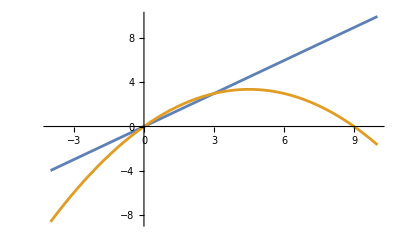

```mathematica
Plot[{x,(9-x)*x/6},{x,-4,10}]
(*Za x med 0 do 3 konvergira k 3*)
```

```mathematica
{{x->0},{x->3}}
```

4. Poišči vsa realna števila , za katera konvergira vrsta 

.

(x (n+x^(2 n)))/(1+n+x^(2+2 n))

ConditionalExpression[1/x, x∈ℝ&&Log[x]>0]

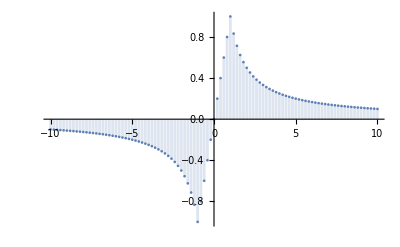

```mathematica
ClearAll[a]
a[n_]:=x^n/(x^(2n)+n)
kvoc=a[n+1]/a[n]//FullSimplify
Limit[kvoc, n->∞]
DiscretePlot[Limit[kvoc, n->∞], {x,-10,10,1/5}]
```

## 3. kolokvij iz Matematike 1

-Graphics-